## Day 1 afternoon — corrections

## Exercise 1: selection on aggressivity

```mathematica
Clear["Global`*"]
```

```mathematica
P[y_,x_]=1/2 V (1-x)+y (V/2-C x);
f[y_,x_]:=f0+δ P[y,x];
ρ=s+((1-s) f[y,x])/f[x,x];
```

### d. Selection gradient

```mathematica
S=Simplify[D[ρ,y]/.y->x]
```

-((-1+s) (V-2 C x) δ)/(2 f0+(V-2 C x^2) δ)

```mathematica
selectionWhenLow=FullSimplify[S>0]
```

(-1+s) (V-2 C x) δ (2 f0+(V-2 C x^2) δ)<0

Selection favours increasing aggressivity below the threshold V/(2 C) and decreasing aggressivity above it.

### e. Gradual evolution

```mathematica
sing=Flatten[Solve[S==0,x]]
```

{x→V/(2 C)}

```mathematica
xstar=x/.sing
```

V/(2 C)

```mathematica
interiorCondition=FullSimplify[0<xstar<1,Assumptions->{V>0,C>0}]
```

V<2 C

```mathematica
J=FullSimplify[D[S,x]/.sing ] ;
%* f[x,x]/.sing //Simplify
(* we can multiply by f[x,x]>0 to make expressions look better *)
```

C (-1+s) δ

J is negative, so the singular strategy is convergence stable.

```mathematica
effectOfV=Simplify[D[xstar,V]];
effectOfC=Simplify[D[xstar,C]];
{effectOfV,effectOfC}
```

{1/(2 C),-V/(2 C^2)}

A more valuable resource increases evolved aggressivity, whereas a larger fighting cost decreases it.

```mathematica
ρ-1 //Simplify
D[%,s]
```

((-1+s) (V-2 C x) (x-y) δ)/(2 f0+(V-2 C x^2) δ)

((V-2 C x) (x-y) δ)/(2 f0+(V-2 C x^2) δ)

Mutant growth rate is proportional to 1 - s. So higher survival weakens selection without changing its direction.

### f. Evolution and population size

```mathematica
Nhat=Simplify[(f[x,x]/(1-s)-1)/γ]
```

-(-2+2 f0+2 s+V δ-2 C x^2 δ)/(2 (-1+s) γ)

```mathematica
NhatPrime=Factor[D[Nhat,x]]
```

(2 C x δ)/((-1+s) γ)

For x > 0, equilibrium population size decreases as aggressivity increases. So Starting below xstar, selection increases aggressivity while population size decreases.

```mathematica
changeInPopulationSize=FullSimplify[(Nhat/.x->xstar)-(Nhat/.x->0)]
```

-(V^2 δ)/(4 C γ-4 C s γ)

Selection favours individuals that gain more from contests against current residents. Mutual aggression lowers fecundity, so this individual advantage reduces population size.

## Exercise 3: cooperative hunting

```mathematica
Clear["Global`*"]
```

### a. Payoff, demography and invasion fitness

```mathematica
payoffCC=y x 2;
payoffCS=y (1-x) 0;
payoffSC=(1-y) x;
payoffSS=(1-y) (1-x);
P[y_,x_]=Simplify[payoffCC+payoffCS+payoffSC+payoffSS]
```

1+(-1+2 x) y

```mathematica
f[y_,x_]:=2+P[y,x]
```

```mathematica
residentRecursion=Nt1==(s+f[x,x]/(1+γ Nt)) Nt;
equilibria=Simplify[Solve[residentRecursion/.Nt1->Nt,Nt]]
```

{{Nt→0},{Nt→(2+s-x+2 x^2)/(γ-s γ)}}

```mathematica
Nhat=Simplify[(f[x,x]/(1-s)-1)/γ]
```

(2+s-x+2 x^2)/(γ-s γ)

```mathematica
ρ=Simplify[s+((1-s) f[y,x])/f[x,x]]
```

s+((1-s) (3+(-1+2 x) y))/(3+x (-1+2 x))

```mathematica
Simplify[(ρ/.y->x)==1]
```

True

### b. Phenotypic evolution

```mathematica
S=Simplify[D[ρ, y]/.y->x]
```

((1-s) (-1+2 x))/(3+x (-1+2 x))

```mathematica
sing=Flatten[Solve[S==0,x]]
```

{x→1/2}

```mathematica
J=FullSimplify[D[S, x]/.sing]
```

-2/3 (-1+s)

J is positive, so the interior singular strategy is not convergence stable.

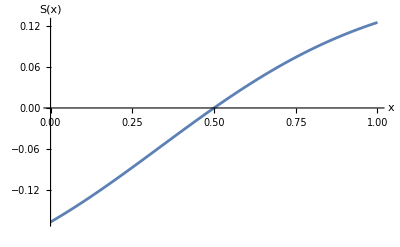

```mathematica
Plot[Evaluate[S/.s->1/2],{x,0,1},AxesLabel->{"x","S(x)"},PlotRange->All]
```

### c. Two evolutionary outcomes

```mathematica
NhatSolitary=Simplify[Nhat/.x->0];
NhatCooperative=Simplify[Nhat/.x->1];
populationDifference=Simplify[NhatCooperative-NhatSolitary];
{NhatSolitary,NhatCooperative,populationDifference}
```

{(2+s)/(γ-s γ),(3+s)/(γ-s γ),1/(γ-s γ)}

Completely cooperative hunting supports the larger population.

For x < 1/2, selection drives the population towards solitary hunting. For x > 1/2, selection drives it towards cooperative hunting.

Cooperation succeeds only when the partner also cooperates. This positive frequency dependence makes xstar an evolutionary threshold and generates bistability.